# Modelling a Submarine Using Potential Flow Analysis

Potential flow analysis can be used to model a variety of objects, and how they interact with fluid flows.

## Uniform Flow

The most basic potential flow regime is a uniform stream in the x direction.

Let’s model a stream with velocity U=5:

```mathematica
U=5;
```

The following are the stream function and velocity potential, respectively:

```mathematica
ψuniform[y_]=U y;
ϕuniform[x_]=U x;
```

Finding the x and y components of the velocity is trivial in this case, but it will help with understanding a more complex flow later.

To find the x component of the velocity of the stream, we take the derivative of the velocity potential with respect to x:

```mathematica
u=D[ϕuniform[x],x]
```

5

To find the y component, we take the negative derivative of the stream function with respect to y:

```mathematica
v=-D[ψuniform[x],y]
```

0

Now let’s plot the stream lines of the flow:

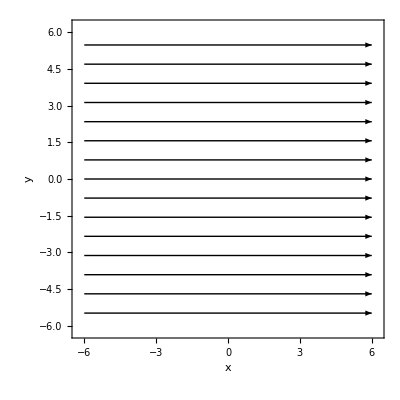

```mathematica
StreamPlot[
{u,v},{x,-6,6},{y,-6,6},
StreamScale->Full,
FrameLabel->{x,y},
StreamStyle->{Arrowheads[.03],Black}
]
```

## Source or Sink at the Origin

The next potential flow regime we will need is a source (or sink) at the origin.  In either case, the z axis is treated as an infinitesimally thin pipe manifold, through which fluid is ejected (or sucked in) at volume flow rate Q that is uniform along its length b.

Let’s model a source at the origin with the following values for volume flow rate and length:

```mathematica
Q=2000;
b=200;
```

The source will have strength m, defined by:

```mathematica
m=Q/(2 π b);
```

At a given position (x,y), the velocity potential will be:

```mathematica
ϕsource[x_,y_]=m Log[√(x^2+y^2)];
```

and the stream function will be:

```mathematica
ψsource[x_,y_]=m ArcTan[y/x];
```

From here, we can find the x and y velocity components via derivation:

```mathematica
𝓊[x_,y_]=D[ψsource[x,y],y];
𝓋[x_,y_]=D[ϕsource[x,y],y];
```

Let us now make a plot of the stream lines:

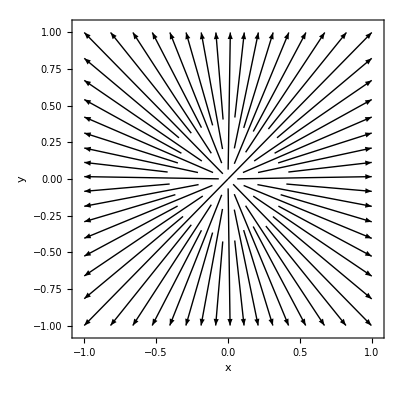

```mathematica
StreamPlot[
{𝓊[x,y],𝓋[x,y]},{x,-1,1},{y,-1,1},
StreamScale->Full,FrameLabel->{x,y},
StreamStyle->{Arrowheads[.03],Black}
]
```

## Rankine Half-Body

A good way to model a submarine moving through water is to approximate the submarine as a Rankine half-body shape.  This is the shape that occurs when a uniform flow encounters a single source.  We can use our uniform flow and source from above.

We first define the x velocity component by adding together the x velocity components for the uniform stream and source:

```mathematica
𝕦[x_,y_]=u+𝓊[x,y];
```

Likewise, we define the y velocity component by adding together the y velocity components for the uniform stream and source:

```mathematica
𝕧[x_,y_]=v+𝓋[x,y];
```

Before plotting the streamlines, we should make a list of points that we want the streamlines to go through:

```mathematica
points=({{-0.5, -0.5}, {-0.5, 0}, {-0.5, 0.5}, {-0.25, -0.5}, {-.25, 0}, {-0.25, 0.5}, {0, -0.5}, {0, 0}, {0, 0.25}, {0, -.25}, {0, 0.5}, {.25, -.5}, {0.25, -0.25}, {0.25, 0}, {0.25, 0.25}, {0.25, 0.5}, {0.5, -0.5}, {0.5, 0}, {0.5, 0.5}, {-.25, .25}, {-.25, -.25}});
```

Now, let’s plot the streamlines:

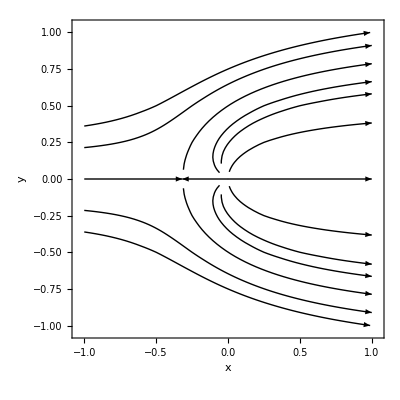

```mathematica
StreamPlot[
{𝕦[x,y],𝕧[x,y]},{x,-1,1},{y,-1,1},
StreamScale->Full,
FrameLabel->{x,y},
StreamStyle->{Arrowheads[.03],Black},
StreamPoints->points
]
```

As we can see, the streamlines form a roughly elliptical half-body shape.  At the nose of the body is a stagnation point, where the flow velocity is zero.  This shape represents the upstream end of our submarine moving through the water.

To make the visualization even more clear, we can omit the streamlines that are “inside” the submarine by specifying new points for the streamlines to go through:

```mathematica
newPoints=({{-0.5, -0.5}, {-0.5, 0}, {-0.5, 0.5}, {-0.25, -0.5}, {-0.25, 0.5}, {0, -0.5}, {0, -.25}, {-.25, .25}, {-.25, -.25}, {-.75, .5}, {-.75, -.5}});
```

Our new plot shows only the streamlines defining the nose of the submarine, and the water passing around it:

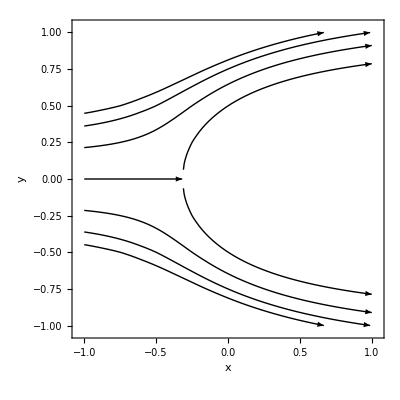

```mathematica
StreamPlot[
{𝕦[x,y],𝕧[x,y]},{x,-1,1},{y,-1,1},
StreamScale->Full,
FrameLabel->{x,y},
StreamStyle->{Arrowheads[.03],Black},
StreamPoints->newPoints
]
```

Further Explorations

Try modeling a symmetrical airfoil using a series of sinks and sources in a uniform flow

Try modeling an airfoil in a uniform stream near the ground by using an image airfoil

Authorship information

Kaleb Alekel

6-21-17

ka5@geneseo.edu